### Squeezed output 2019/08/30 2019/06/03

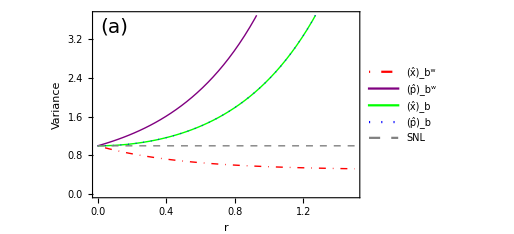

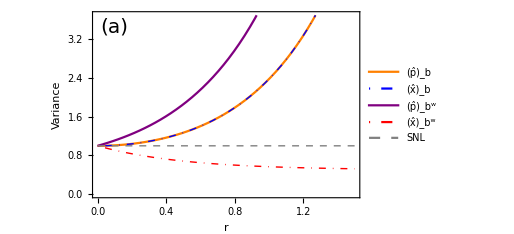

```mathematica
n=50;(* number od modes *)
fX2=1+n/(n s)(Cosh[2r] - 1);(* Without wavefront shaping*)
fP2=fX2;(* Without wavefront shaping*)
flucX2=1-n/(n s)(1-ⅇ^(-2r));(* With wavefront shaping*)
flucP2=1+n/(n s)(ⅇ^(2r)-1);(* With wavefront shaping*)
fig1=Plot[{flucX2/.s->2,flucP2/.s->2,fX2/.s->2,fP2/.s->2,r-r+1},{r,0,1.5},PlotStyle->{{DotDashed,Red,Thick},{Purple,Thick},{Green,Thick},{Dotted,Blue,Thick},{Gray,Dashed,Thick}},PlotLegends->Placed[{Style["(x̂)_b^w",FontSize->14],Style["(p̂)_b^w",FontSize->14],Style["(x̂)_b",FontSize->14],Style["(p̂)_b",FontSize->14],Style["SNL",FontSize->12.5]},{{0.89,0.58}}],Frame->True, FrameLabel->{Style["r",FontSize->20],Text[Style["Variance",FontSize->20]]},FrameTicksStyle->Directive[14.5],PlotRange->{{0,3.7}},Epilog->{Text[Style["(a)",FontSize->20],Scaled[{.08,.92}]](*,Text[Style["SNL",FontSize->14],Scaled[{.88,.33}]],Text[Style["(x̂)_b^w",FontSize->14],Scaled[{.6,.08}]],Text[Style["(p̂)_b^w",FontSize->14],Scaled[{.45,.88}]],,Text[Style["(x̂)_b",FontSize->14],Scaled[{.9,.88}]],Text[Style["(p̂)_b",FontSize->14],Scaled[{.82,.7}]]*)},ImageSize->{380,280}]
```

```mathematica
Export["E:\\MT\\00_Researching\\03_PUF\\03_Security_PUF\\05_New_scheme\\09_Squeezing_focused_light\\03_Code\\00_Figures\\dx2r20190604.eps",fig1]
```

E:\MT\00_Researching\03_PUF\03_Security_PUF\05_New_scheme\09_Squeezing_focused_light\03_Code\00_Figures\dx2r20190604.eps

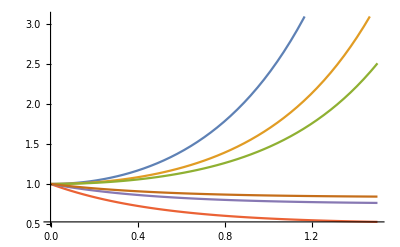

```mathematica
Plot[{fX2/.s->2,fX2/.s->4,fX2/.s->6,flucX2/.s->2,flucX2/.s->4,flucX2/.s->6},{r,0,1.5}]
```

```mathematica
Plot[{sen2^(1/2)/.{t1->.9,g->g0},sen2^(1/2)/.{t1->.95,g->g0},sen2^(1/2)/.{t1->1,g->g0},SNL/.g->g0,HL/.g->g0},{p1,-1,1},PlotRange->{0,1.5},PlotStyle->{{Dashed,Blue},{Dotted,Red,Thick},Black,{Dotted,Green,Thick},DotDashed},PlotLabel->Style["|0>+|0>",16,Red],PlotLegends->Placed[{"L = 0.1","L = 0.05","L = 0","SNL","HL"},{{1,0.7}}],Frame->True, FrameLabel->{Style["ϕ",FontSize->18],Text[Style["Δϕ",FontSize->18]]}]
```

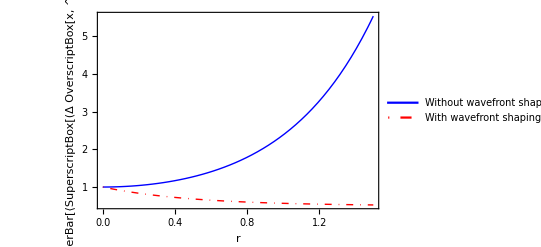

```mathematica
fig1=Plot[{fX2/.s->2,flucX2/.s->2},{r,0,1.5},PlotStyle->{{Blue,Thick},{DotDashed,Red,Thick}},PlotLegends->Placed[{Style["Without wavefront shaping",FontSize->14],Style["With wavefront shaping",FontSize->14]},{{0.4,0.8}}],Frame->True, FrameLabel->{Style["r",FontSize->20],Text[Style["OverBar[⟨SuperscriptBox[(Δ OverscriptBox[x, ^]), 2]⟩]",FontSize->20]]},FrameTicksStyle->Directive[14.5]]
```

```mathematica
Export["E:\\MT\\00_Researching\\03_PUF\\03_Security_PUF\\05_New_scheme\\09_Squeezing_focused_light\\03_Code\\00_Figures\\dx2r20190604.eps",fig1](*ImageResolution->300,ImageSize->{480,480}];*)
```

E:\MT\00_Researching\03_PUF\03_Security_PUF\05_New_scheme\09_Squeezing_focused_light\03_Code\00_Figures\dx2r20190604.eps

```mathematica
∫_0^∞ x/a^2 ⅇ^(-x^2/(2 a^2))ⅆx
```

ConditionalExpression[1,Re[a^2]>0]

```mathematica
f1=Simplify[∫_0^∞ x^(3/2)/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

2^(1/4) √a Gamma[5/4]

a √(π/2)

2 a^2

π/4

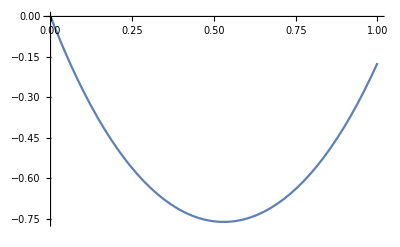

```mathematica
f2=Simplify[∫_0^∞ x^2/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
f4=Simplify[∫_0^∞ x^3/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
ratio=f2^2/f4  
diff=4Sinh[r](Sinh[r]-ratio Cosh[r]);
Plot[diff,{r,0,1}]
```

```mathematica
f4=Simplify[∫_0^∞ x^3/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

2 a^2

```mathematica
f5=Simplify[∫_0^∞ x^4/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

3 a^3 √(π/2)

```mathematica
f6=Simplify[∫_0^∞ x^5/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

8 a^4

```mathematica
f6/f4^2
```

2

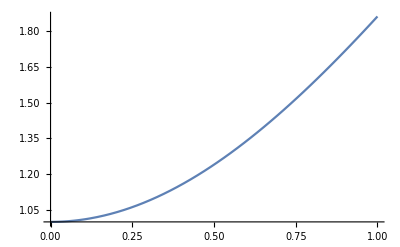

```mathematica
g=1/2 ⅇ^(-a^2) (2+a ⅇ^(a^2) √π+a ⅇ^(a^2) √π Erf[a]-a ⅇ^(a^2) √π Erfc[a]);
Plot[g,{a,0,1}]
```

1/2 (1+2 a^2) √π

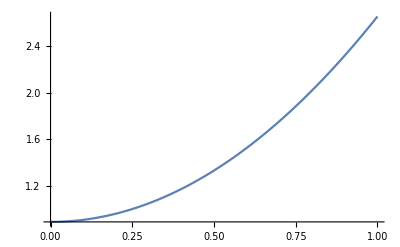

```mathematica
f1=1/(√π)∫_(-∞)^∞ x^2 ⅇ^(-(x-a)^2)ⅆx
Plot[f1,{a,0,1}]
```

```mathematica
norm=1/(√π)∫_(-∞)^∞ ⅇ^(-(x-a)^2)ⅆx
```

√π

1/4 (3+4 a^2 (3+a^2)) √π

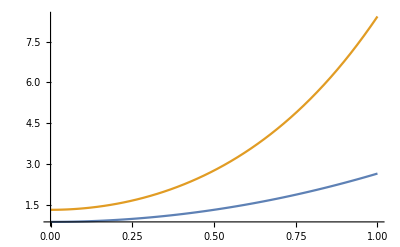

```mathematica
f2=∫_(-∞)^∞ x^4 ⅇ^(-(x-a)^2)ⅆx
Plot[{f1,f2},{a,0,1}]
```

```mathematica
√π f2/f1^2//Expand
```

3/((1+2 a^2)^2)+(12 a^2)/((1+2 a^2)^2)+(4 a^4)/((1+2 a^2)^2)